TemporalData::rsmplng: 数据没有均匀间隔，并且将自动采样到最小时间增量的解决方案 .

TimeSeriesModel[…]

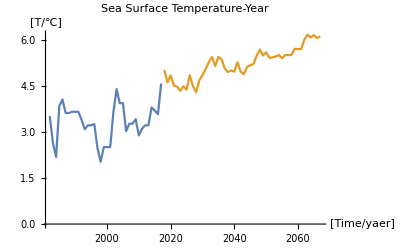

```mathematica
data1={{1982,3.52},{1983,2.64},{1984,2.19},{1985,3.85},{1986,4.06},{1987,3.62},{1989,3.66},{1992,3.4},{1993,3.09},{1994,3.22},{1996,3.26},{1997,2.48},{1998,2.03},{1999,2.51},{2002,3.64},{2003,4.4},{2004,3.94},{2006,3.03},{2007,3.27},{2009,3.42},{2010,2.89},{2011,3.11},{2012,3.22},{2014,3.8},{2015,3.7},{2016,3.58},{2017,4.58}};
tsm=TimeSeriesModelFit[data1,{"SARIMA",{{2,1,2},{4,0,2},5}}]
ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{50}]},AxesLabel->{RawBoxes[RowBox[{"[",RowBox[{"Time","/","yaer"}],"]"}]],RawBoxes[RowBox[{"[",RowBox[{"T","/","℃"}],"]"}]]},PlotLabel->HoldForm[Sea Surface Temperature-Year],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]}]
```

```mathematica
Do[Print[tsm[2017+10*n]],{n,1,5}]
```

4.49777

5.07004

5.48091

5.50575

6.11749

63.2888-0.915 x

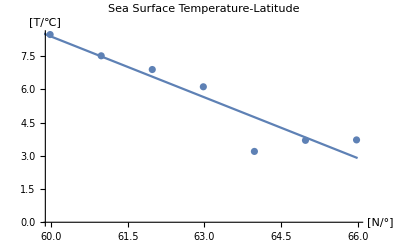

```mathematica
data2={{59.97917,8.48},{60.97917,7.52},{61.97917,6.9},{62.97917,6.12},{63.97917,3.2},{64.97917,3.7},{65.97917,3.72}};
n=Fit[data2,{1,x},x](*R^2=0.8741*)
Show[ListPlot[data2],Plot[n,{x,59,66}],AxesLabel->{RawBoxes[RowBox[{"[",RowBox[{"N","/","°"}],"]"}]],RawBoxes[RowBox[{"[",RowBox[{"T","/","℃"}],"]"}]]},PlotLabel->HoldForm[Sea Surface Temperature-Latitude],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]}]
```

10645.3-60.6803 x+0.086489 x^2

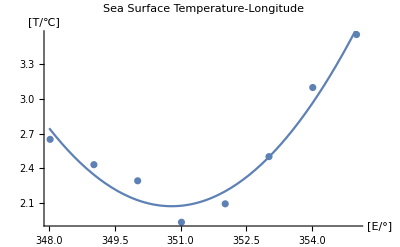

```mathematica
data3={{348.02084,2.65},{349.02084,2.43},{350.0208,2.29},{351.0208,1.93},{352.0208,2.09},{353.0208,2.5},{354.0208,3.1},{355.0208,3.56}};
w=Fit[data3,{1,x,x^2},x](*R^2=0.9522*)
Show[ListPlot[data3],Plot[w,{x,348,355}],AxesLabel->{RawBoxes[RowBox[{"[",RowBox[{"E","/","°"}],"]"}]],RawBoxes[RowBox[{"[",RowBox[{"T","/","℃"}],"]"}]]},PlotLabel->HoldForm[Sea Surface Temperature-Longitude],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]}]
```

```mathematica
f=63.2888-0.915 x+10645.3-60.6803 y+0.086489 y^2
```

10708.6-0.915 x-60.6803 y+0.086489 y^2

```mathematica
Plot3D[f,{x,59,66},{y,348,355}]
```

-Graphics3D-

```mathematica
(*59 355*)
a[x_,y_]=tsm[2017]+0.915*65-0.915*x+60.6803*356-0.086489*356^2-60.6803 y+0.086489 y^2;
a[59,355]
```

9.25662

```mathematica
Plot[{x=(a[59,355]-(0.915*65+60.6803*356-0.086489*356^2-60.6803 y+0.086489 y^2+tsm[2017]))/(-0.915),
x=(a[59,355]-(0.915*65+60.6803*356-0.086489*356^2-60.6803 y+0.086489 y^2+tsm[2027]))/(-0.915),
x=(a[59,355]-(0.915*65+60.6803*356-0.086489*356^2-60.6803 y+0.086489 y^2+tsm[2037]))/(-0.915),
x=(a[59,355]-(0.915*65+60.6803*356-0.086489*356^2-60.6803 y+0.086489 y^2+tsm[2047]))/(-0.915),
x=(a[59,355]-(0.915*65+60.6803*356-0.086489*356^2-60.6803 y+0.086489 y^2+tsm[2057]))/(-0.915),
x=(a[59,355]-(0.915*65+60.6803*356-0.086489*356^2-60.6803 y+0.086489 y^2+tsm[2067]))/(-0.915)},{y,347,356},PlotLegends->{"2017","2027","2037","2047","2057","2067"},AxesLabel->{RawBoxes[RowBox[{"[",RowBox[{"N","/","°"}],"]"}]],RawBoxes[RowBox[{"[",RowBox[{"N","/","°"}],"]"}]]},PlotLabel->HoldForm[Latitude-Longitude],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]}]
```

```mathematica
GeoGraphics[{EdgeForm[Black],FaceForm[Red],Polygon[LinguisticAssistant]},GeoRange->{{55,65},{-15,0}}]
```